## Stark shifts in the FORT

#### Polarizabilities obtained from T.G. Walker.

For the 5p3/2 state 1064 nm light:

```mathematica
ϵ0 = 8.854*10^-12;
h = 6.626*10^-34;
c = 2.9987*10^8;
kB = 1.3807*10^-23;
```

```mathematica
leakage = .05 ;(*percentage of total FORT power getting to atoms; e.g. leakage is about .05*)
```

```mathematica
α05pThreeHalves = 4 π ϵ0*10^-6*-143.77*10^-24;
α25pThreeHalves = 4 π ϵ0 *10^-6*74.44*10^-24; (*SI units*)
```

```mathematica
Uac[F_,mF_,J_,i_,E_,α0_,α2_]:= -1/4 α0 E^2-1/4 α2 E^2(3 mF^2-F(F+1))/(F(2F-1)) (3 (F(F+1)+J(J+1)−i(i+1))((F(F+1)+J(J+1)−i(i+1)) - 1) - 4F(F+1)J(J+1))/((2 F +2)(2F+3) J (2 J -1));
cgsToSI[α_]:=4π ϵ0*10^-6 α;
JToMHz[U_]:= U/(h*10^6);
```

```mathematica
Efield[P_] := ((4P)/(c ϵ0 π w0^2))^(1/2);
```

```mathematica
P = .384*.4; 
w0 = 2.5*10^-6;
```

```mathematica
JToMHz[Uac[3,0,3/2,3/2,Efield[.05*P],α05pThreeHalves,α25pThreeHalves]]
```

6.54907

```mathematica
130.98147943795067 (*MHz*)
```

130.981

For the 5s1/2 state 1064 nm light:

```mathematica
α05sOneHalf = cgsToSI[97*10^-24]
```

1.07925×10^-38

```mathematica
GroundStateShift = JToMHz[-1/4 α05sOneHalf Efield[P]^2]
```

-2.39954

#### Differential AC Stark shifts on D2 cooling transition

```mathematica
DiffACShifts = Table[{mF,JToMHz[Uac[3,mF,3/2,3/2,Efield[P],α05pThreeHalves,α25pThreeHalves]]-GroundStateShift},{mF,-3,3}]
```

{{-3,36.7006},{-2,73.5299},{-1,95.6275},{0,102.993},{1,95.6275},{2,73.5299},{3,36.7006}}

The light shifts for theses transitions are positive, and the PGC light seen from the atoms perspective is an additional 166-204 MHz detuned at for 500 mW at the atoms, and 40% of this at the center trap

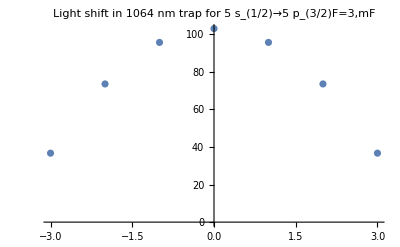

```mathematica
ListPlot[DiffACShifts,PlotRange->Full,PlotLabel->"Light shift in 1064 nm trap for 5 s_(1/2)→5 p_(3/2)F=3,mF"]
```

For different powers:

```mathematica
(*Table[ListPlot[Table[{mF,JToMHz[Uac[3,mF,3/2,3/2,Efield[.4*P],α05pThreeHalves,α25pThreeHalves]]-GroundStateShift},{mF,-3,3}]],{P,{.2,.3,.4,.5}}]*)
```

#### Excited state shifts only

Shifts with only 5% power leaking through the AOM.

```mathematica
leakage = .05
```

0.05

```mathematica
ExcitedACShifts=Table[{mF,JToMHz[Uac[3,mF,3/2,3/2,Efield[leakage*P],α05pThreeHalves,α25pThreeHalves]]},{mF,-3,3}]
```

{{-3,1.71505},{-2,3.55652},{-1,4.6614},{0,5.02969},{1,4.6614},{2,3.55652},{3,1.71505}}

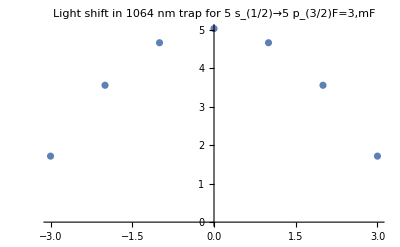

```mathematica
ListPlot[ExcitedACShifts,PlotRange->Full,PlotLabel->"Light shift in 1064 nm trap for 5 s_(1/2)→5 p_(3/2)F=3,mF"]
```

These Stark shifts are all positive so atoms left in the excited state will be repulsed by the FORT. When chopping the FORT and RO alternately it is critical that the RO light is turned off for at least one lifetime (~ .16 μs) of the excited state so that the atoms decay to the ground state before the FORT is turned back on.

#### FORT trap depth

```mathematica
r2power = .4*.384 ;(*40% in 0 order, 384 mW measured before Jenoptik*)
```

```mathematica
GroundStateShiftJ = -1/4 α05sOneHalf Efield[r2power]^2(*[J]*)
```

-3.17987×10^-26

```mathematica
Tdepth = -1000*GroundStateShiftJ/kB (*the FORT "depth" in [mK]*)
```

2.30309

Mark’s example for Cs

```mathematica
Ef= ((4 (.01))/(c ϵ0 π (10^-6)^2))^(1/2);
```

```mathematica
-1/4 cgsToSI[(168*10^-24)] Ef^2
```

-2.24097×10^-26

#### Atom escape times

Suppose an atom has some temperature T, in a trap of radius w0? What is the shortest time it will take the atom to move outside of the beam cross-section (perpendicular to the optical axis) if the beam is turned off?

```mathematica
vRMS[T_]:= √((2 kB T)/m); m =
```